## Variables

```mathematica
Clear[N1];Clear[N2];Clear[x1];
```

## Parameters

```mathematica
Clear[x2];Clear[xopt];
Clear[lambdaMax01];Clear[lambdaMax02];Clear[lambdaMaxVal];Clear[betaMax];
```

## Base equation

### Demography

```mathematica
N1tPlus1=(lambdaMax01 Exp[-(x1-xopt)^2]N1)/(1+N1+betaMax Exp[-(x2-x1)^2] N2);
N1tPlus1N1=(lambdaMax01 Exp[-(x1-xopt)^2])/(1+N1+betaMax Exp[-(x2-x1)^2] N2);
N2tPlus1=(lambdaMax02 Exp[-(x2-xopt)^2]N2)/(1+N2+betaMax Exp[-(x1-x2)^2]N1);
```

```mathematica
N1tPlus1Appr=(lambdaMax01 Exp[-(x1-xopt)^2]N1)/(N1+betaMax Exp[-(x2-x1)^2] N2);
N2tPlus1Appr=(lambdaMax02 Exp[-(x2-xopt)^2]N2)/(N2+betaMax Exp[-(x1-x2)^2]N1);
```

### Evolution

```mathematica
x1tPlus1=x1+G D[Log[N1tPlus1N1],x1]//Simplify
```

(-ⅇ^((x1-x2)^2) (1+N1) ((-1+2 G) x1-2 G xopt)+betaMax N2 (x1+2 G (-x2+xopt)))/(ⅇ^((x1-x2)^2) (1+N1)+betaMax N2)

### Frequency of species 1

```mathematica
M1tPlus1=N1tPlus1Appr/(N1tPlus1Appr+N2tPlus1Appr)//Simplify;
M1tPlus1=M1tPlus1/.{N1->M1,N2->1-M1};
M1tPlus1M1=M1tPlus1-M1//Simplify
```

M1 (-1+(ⅇ^((x2-xopt)^2) lambdaMax01 (ⅇ^((x1-x2)^2) (-1+M1)-betaMax M1))/(ⅇ^((x1-x2)^2) (ⅇ^((x2-xopt)^2) lambdaMax01+ⅇ^((x1-xopt)^2) lambdaMax02) (-1+M1) M1-betaMax (ⅇ^((x1-xopt)^2) lambdaMax02 (-1+M1)^2+ⅇ^((x2-xopt)^2) lambdaMax01 M1^2)))

```mathematica
M1tPlus1M1=(-1+(ⅇ^((x2-xopt)^2) lambdaMax01 (ⅇ^((x1-x2)^2) (-1+M1)-betaMax M1))/(ⅇ^((x1-x2)^2) (ⅇ^((x2-xopt)^2) lambdaMax01+ⅇ^((x1-xopt)^2) lambdaMax02) (-1+M1) M1-betaMax (ⅇ^((x1-xopt)^2) lambdaMax02 (-1+M1)^2+ⅇ^((x2-xopt)^2) lambdaMax01 M1^2)))
```

-1+(ⅇ^((x2-xopt)^2) lambdaMax01 (ⅇ^((x1-x2)^2) (-1+M1)-betaMax M1))/(ⅇ^((x1-x2)^2) (ⅇ^((x2-xopt)^2) lambdaMax01+ⅇ^((x1-xopt)^2) lambdaMax02) (-1+M1) M1-betaMax (ⅇ^((x1-xopt)^2) lambdaMax02 (-1+M1)^2+ⅇ^((x2-xopt)^2) lambdaMax01 M1^2))

```mathematica
x1tPlus1x1=D[Log[N1tPlus1Appr],x1]//Simplify;
x1tPlus1x1=x1tPlus1x1/.{N1->M1,N2->1-M1}
```

(-2 ⅇ^((x1-x2)^2) M1 (x1-xopt)+2 betaMax (1-M1) (-x2+xopt))/(betaMax (1-M1)+ⅇ^((x1-x2)^2) M1)

```mathematica
par={x2->-0.1,xopt->0,lambdaMax01->5,lambdaMax02->5,betaMax->1.1,G->0.001};fr01=FindRoot[{(M1tPlus1M1/.par)==0,(x1tPlus1x1/.par)==0},{M1,0.1},{x1,0.8}]
```

{M1→0.0547311,x1→0.817977}

## Figure (a, b) Nullclines of frequency dynamics of species 1 and trait dynamics of species 1

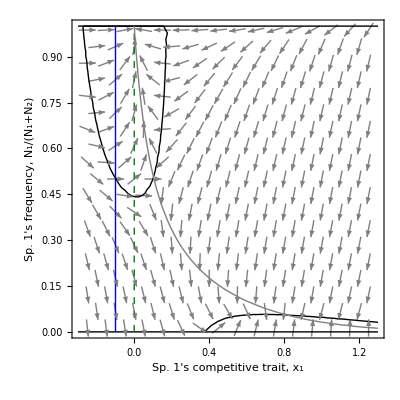

```mathematica
par={x2->-0.1,xopt->0,lambdaMax01->100,lambdaMax02->100,betaMax->1.1,G->0.1};
Show[
VectorPlot[{(G x1tPlus1x1/.par),(M1tPlus1M1/.par)},{x1,-0.3,1.3},{M1,0,1},VectorStyle->Gray,VectorColorFunction->None],
Graphics[{Black,Thick,Line[{{-0.3,1},{1.3,1}}]}],
Graphics[{Black,Thick,Line[{{-0.3,0},{1.3,0}}]}],
Graphics[{RGBColor[0,0.5,0],Thick,Dashed,Line[{{0,0},{0,1}}]}],
Graphics[{RGBColor[0,0,1],Thick,Line[{{-0.1,0},{-0.1,1}}]}],
ContourPlot[{(M1tPlus1M1/.par)==0,(x1tPlus1x1/.par)==0},{x1,-0.3,1.3},{M1,0,1},ContourStyle->{{Black,Thick},{Gray,Thick}}],FrameLabel->{{RawBoxes[RowBox[{RowBox[{RowBox[{"Sp","."," ",RowBox[{"1","'"}]}],"s"," ","frequency"}],","," ",RowBox[{SubscriptBox[StyleBox["N",FontSlant->"Italic"],"1"],"/",RowBox[{"(",RowBox[{SubscriptBox[StyleBox["N",FontSlant->"Italic"],"1"],"+",SubscriptBox[StyleBox["N",FontSlant->"Italic"],"2"]}],")"}]}]}]],None},{RawBoxes[RowBox[{RowBox[{RowBox[{"Sp","."," ",RowBox[{"1","'"}]}],"s"," ","competitive"," ","trait"}],","," ",SubscriptBox[StyleBox["x",FontSlant->"Italic"],"1"]}]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

```mathematica
par={x2->-0.1,xopt->0,lambdaMax01->5,lambdaMax02->5,betaMax->1.1,G->0.1};
Show[
VectorPlot[{(G x1tPlus1x1/.par),(M1tPlus1M1/.par)},{x1,-0.3,1.3},{M1,0,1},VectorStyle->Gray,VectorColorFunction->None],
Graphics[{Black,Thick,Line[{{-0.3,1},{1.3,1}}]}],
Graphics[{Black,Thick,Line[{{-0.3,0},{1.3,0}}]}],
Graphics[{RGBColor[0,0.5,0],Thick,Dashed,Line[{{0,0},{0,1}}]}],
Graphics[{RGBColor[0,0,1],Thick,Line[{{-0.1,0},{-0.1,1}}]}],
ContourPlot[{(M1tPlus1M1/.par)==0,(x1tPlus1x1/.par)==0},{x1,-0.3,1.3},{M1,0,1},ContourStyle->{{Black,Thick},{Gray,Thick}}],FrameLabel->{{RawBoxes[RowBox[{RowBox[{RowBox[{"Sp","."," ",RowBox[{"1","'"}]}],"s"," ","frequency"}],","," ",RowBox[{SubscriptBox[StyleBox["N",FontSlant->"Italic"],"1"],"/",RowBox[{"(",RowBox[{SubscriptBox[StyleBox["N",FontSlant->"Italic"],"1"],"+",SubscriptBox[StyleBox["N",FontSlant->"Italic"],"2"]}],")"}]}]}]],None},{RawBoxes[RowBox[{RowBox[{RowBox[{"Sp","."," ",RowBox[{"1","'"}]}],"s"," ","competitive"," ","trait"}],","," ",SubscriptBox[StyleBox["x",FontSlant->"Italic"],"1"]}]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

-Graphics-

## Figure (c) FindRoot (Frequency dynamics of species 1)

```mathematica
reps=101;
M1res01List=Table[NA,{i,2 reps-1}];x1res01FreqList=Table[NA,{i,2 reps-1}];
```

```mathematica
lambdaMaxMax=200;lambdaMaxMin=100;
For[i=1,i<=reps,i++,
Print["i = "<>ToString[i]];
lambdaMaxVal=lambdaMaxMin+(lambdaMaxMax-lambdaMaxMin)(i-1)/(reps-1);
par={x2->-0.1,xopt->0,lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal,betaMax->1.1,G->0.001};
If[i==1,
fr01=FindRoot[{(M1tPlus1M1/.par)==0,(x1tPlus1x1/.par)==0},{M1,0.1},{x1,0.8}],
fr01=FindRoot[{(M1tPlus1M1/.par)==0,(x1tPlus1x1/.par)==0},{M1,M1res01},{x1,x1res01}]
];
M1res01=Round[fr01[[1,2]],0.0001];
x1res01=Round[fr01[[2,2]],0.0001];

M1res01List[[i-1+reps]]=M1res01;
x1res01FreqList[[i-1+reps]]=x1res01;
]
```

i = 1

i = 2

i = 3

i = 4

i = 5

i = 6

i = 7

i = 8

i = 9

i = 10

i = 11

i = 12

i = 13

i = 14

i = 15

i = 16

i = 17

i = 18

i = 19

i = 20

i = 21

i = 22

i = 23

i = 24

i = 25

i = 26

i = 27

i = 28

i = 29

i = 30

i = 31

i = 32

i = 33

i = 34

i = 35

i = 36

i = 37

i = 38

i = 39

i = 40

i = 41

i = 42

i = 43

i = 44

i = 45

i = 46

i = 47

i = 48

i = 49

i = 50

i = 51

i = 52

i = 53

i = 54

i = 55

i = 56

i = 57

i = 58

i = 59

i = 60

i = 61

i = 62

i = 63

i = 64

i = 65

i = 66

i = 67

i = 68

i = 69

i = 70

i = 71

i = 72

i = 73

i = 74

i = 75

i = 76

i = 77

i = 78

i = 79

i = 80

i = 81

i = 82

i = 83

i = 84

i = 85

i = 86

i = 87

i = 88

i = 89

i = 90

i = 91

i = 92

i = 93

i = 94

i = 95

i = 96

i = 97

i = 98

i = 99

i = 100

i = 101

```mathematica
lambdaMaxMax=100;lambdaMaxMin=0;

For[i=reps,i>=1,i--,
lambdaMaxVal=lambdaMaxMin+(lambdaMaxMax-lambdaMaxMin)(i-1)/(reps-1);
par={x2->-0.1,xopt->0,lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal,betaMax->1.1,G->0.001};
If[i==reps,fr01=FindRoot[{(M1tPlus1M1/.par)==0,(x1tPlus1x1/.par)==0},{M1,0.1},{x1,0.8}],
fr01=FindRoot[{(M1tPlus1M1/.par)==0,(x1tPlus1x1/.par)==0},{M1,M1res01},{x1,x1res01}]
];
M1res01=Round[fr01[[1,2]],0.0001];x1res01=Round[fr01[[2,2]],0.0001];

M1res01List[[i]]=M1res01;x1res01FreqList[[i]]=x1res01;
]
```

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. (ⅇ^((0.1+x1)^2) (-1+M1)-1.1 M1) ComplexInfinityが見付かりました．

FindRoot::nlnum: {M1,x1} = {0.0547,0.818}において，関数の値{Indeterminate,0.0000949069}は次元{2}の数値のリストではありません．

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. (ⅇ^((0.1+x1)^2) (-1+M1)-1.1 M1) ComplexInfinityが見付かりました．

FindRoot::nlnum: {M1,x1} = {0.0547,0.818}において，関数の値{Indeterminate,0.0000949069}は次元{2}の数値のリストではありません．

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0. (ⅇ^((0.1+x1)^2) (-1+M1)-1.1 M1) ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

FindRoot::nlnum: {M1,x1} = {0.0547,0.818}において，関数の値{Indeterminate,0.0000949069}は次元{2}の数値のリストではありません．

General::stop: この計算中に，FindRoot::nlnumのこれ以上の出力は表示されません．

FindRoot::srect: 検索指定{M1,M1res01}の中の値Round[(0.22 (1-M1)-2 ⅇ^(Plus[«2»]^2) M1 x1)/(1.1 (1+Times[«2»])+ⅇ^Power[«2»] M1)==0,0.0001]が数値でも数値の配列でもありません．

```mathematica
M1res01List
```

## FindRoot (Density dynamics of species 1)

```mathematica
par={x2->-0.1,xopt->0,betaMax->1.1,G->0.001};
```

```mathematica
reps=101;
N1res01List=Table[NA,{i,2 reps-1}];N1res02List=Table[NA,{i,2 reps-1}];
N2res01List=Table[NA,{i,2 reps-1}];N2res02List=Table[NA,{i,2 reps-1}];
x1res01List=Table[NA,{i,2 reps-1}];x1res02List=Table[NA,{i,2 reps-1}];

lambdaMaxMax=200;lambdaMaxMin=100;

For[i=1,i<=reps,i++,
Print["i = "<>ToString[i]];
lambdaMaxVal=lambdaMaxMin+(lambdaMaxMax-lambdaMaxMin)(i-1)/(reps-1);
If[i==1,fr01=FindRoot[{(N1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N1==0,(N2tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N2==0,(x1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-x1==0},{{N1,99},{N2,1},{x1,0.1}}];
fr02=FindRoot[{(N1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N1==0,(N2tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N2==0,(x1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-x1==0},{{N1,5},{N2,95},{x1,0.8}}],
fr01=FindRoot[{(N1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N1==0,(N2tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N2==0,(x1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-x1==0},{{N1,N1res01},{N2,N2res01},{x1,x1res01}}];
fr02=FindRoot[{(N1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N1==0,(N2tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N2==0,(x1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-x1==0},{{N1,N1res02},{N2,N2res02},{x1,x1res02}}]
];
N1res01=Round[fr01[[1,2]],0.0001];N2res01=Round[fr01[[2,2]],0.0001];x1res01=Round[fr01[[3,2]],0.0001];
N1res02=Round[fr02[[1,2]],0.0001];
N2res02=Round[fr02[[2,2]],0.0001];
x1res02=Round[fr02[[3,2]],0.0001];

N1res01List[[i-1+reps]]=N1res01;N1res02List[[i-1+reps]]=N1res02;
N2res01List[[i-1+reps]]=N2res01;N2res02List[[i-1+reps]]=N2res02;
x1res01List[[i-1+reps]]=x1res01;x1res02List[[i-1+reps]]=x1res02;
]
```

i = 1

i = 2

i = 3

i = 4

i = 5

i = 6

i = 7

i = 8

i = 9

i = 10

FindRoot::lstol: 直線探索において刻み幅をAccuracyGoalとPrecisionGoalで指定された許容範囲に減らしましたが，メリット関数に十分な増加が見られませんでした．これらの許容範囲で満足するためには，MachinePrecision桁より高い作業精度が必要となることがあります．

i = 11

i = 12

i = 13

i = 14

i = 15

i = 16

i = 17

i = 18

i = 19

i = 20

i = 21

i = 22

i = 23

i = 24

i = 25

i = 26

i = 27

i = 28

i = 29

i = 30

i = 31

i = 32

i = 33

i = 34

i = 35

i = 36

i = 37

i = 38

i = 39

i = 40

i = 41

i = 42

i = 43

i = 44

i = 45

i = 46

i = 47

i = 48

i = 49

i = 50

i = 51

i = 52

i = 53

i = 54

i = 55

i = 56

i = 57

i = 58

i = 59

i = 60

i = 61

i = 62

i = 63

i = 64

i = 65

i = 66

i = 67

i = 68

i = 69

i = 70

i = 71

i = 72

i = 73

i = 74

i = 75

i = 76

i = 77

i = 78

i = 79

i = 80

i = 81

i = 82

i = 83

i = 84

i = 85

i = 86

i = 87

i = 88

i = 89

i = 90

i = 91

i = 92

i = 93

i = 94

i = 95

i = 96

i = 97

i = 98

i = 99

i = 100

i = 101

```mathematica
lambdaMaxMax=100;lambdaMaxMin=0;

For[i=reps,i>=1,i--,
lambdaMaxVal=lambdaMaxMin+(lambdaMaxMax-lambdaMaxMin)(i-1)/(reps-1);
If[i==reps,fr01=FindRoot[{(N1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N1==0,(N2tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N2==0,(x1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-x1==0},{{N1,99},{N2,1},{x1,0.1}}];
fr02=FindRoot[{(N1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N1==0,(N2tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N2==0,(x1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-x1==0},{{N1,20},{N2,80},{x1,0.8}}],
fr01=FindRoot[{(N1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N1==0,(N2tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N2==0,(x1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-x1==0},{{N1,N1res01},{N2,N2res01},{x1,x1res01}}];
fr02=FindRoot[{(N1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N1==0,(N2tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-N2==0,(x1tPlus1/.par/.{lambdaMax01->lambdaMaxVal,lambdaMax02->lambdaMaxVal})-x1==0},{{N1,N1res02},{N2,N2res02},{x1,x1res02}}]
];
N1res01=Round[fr01[[1,2]],0.0001];N2res01=Round[fr01[[2,2]],0.0001];x1res01=Round[fr01[[3,2]],0.0001];
N1res02=Round[fr02[[1,2]],0.0001];
N2res02=Round[fr02[[2,2]],0.0001];
x1res02=Round[fr02[[3,2]],0.0001];

N1res01List[[i]]=N1res01;N1res02List[[i]]=N1res02;
N2res01List[[i]]=N2res01;N2res02List[[i]]=N2res02;
x1res01List[[i]]=x1res01;x1res02List[[i]]=x1res02;
]
```

FindRoot::lstol: 直線探索において刻み幅をAccuracyGoalとPrecisionGoalで指定された許容範囲に減らしましたが，メリット関数に十分な増加が見られませんでした．これらの許容範囲で満足するためには，MachinePrecision桁より高い作業精度が必要となることがあります．

General::stop: この計算中に，FindRoot::lstolのこれ以上の出力は表示されません．

```mathematica
freq1res01List=Table[NA,{i,2 reps-1}];freq1res02List=Table[NA,{i,2 reps-1}];
Do[freq1res01List[[i]]=N1res01List[[i]]/(N1res01List[[i]]+N2res01List[[i]]),{i,2 reps-1}];
Do[freq1res02List[[i]]=N1res02List[[i]]/(N1res02List[[i]]+N2res02List[[i]]),{i,2 reps-1}];
```

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

```mathematica
x1freq1List01={};x1freq1List02={};
Do[x1freq1List01=Append[x1freq1List01,{x1res01List[[i]],freq1res01List[[i]]}],{i,2 reps-1}];
Do[x1freq1List02=Append[x1freq1List02,{x1res02List[[i]],freq1res02List[[i]]}],{i,2 reps-1}];
```

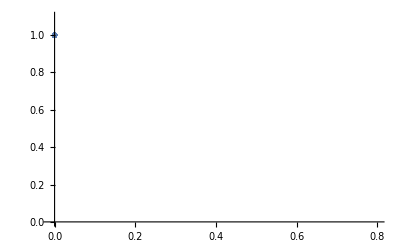

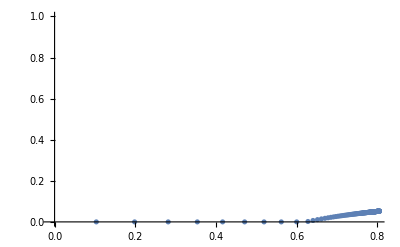

```mathematica
ListPlot[x1freq1List01,PlotRange->{{-0.01,0.8},{0,1.1}}]
ListPlot[x1freq1List02,PlotRange->{{-0.01,0.8},{0,1}}]
```

```mathematica
lambdFreq1res01List=Table[NA,{i,2 reps-1}];lambdFreq1res02List=Table[NA,{i,2 reps-1}];
lambdaMaxMin=10;lambdaMaxMax=190;
Do[freq1res01List[[i]]={lambdaMaxMin+(lambdaMaxMax-lambdaMaxMin)i/(2 reps-1),N1res01List[[i]]/(N1res01List[[i]]+N2res01List[[i]])},{i,2 reps-1}];
Do[freq1res02List[[i]]={lambdaMaxMin+(lambdaMaxMax-lambdaMaxMin)i/(2 reps-1),N1res02List[[i]]/(N1res02List[[i]]+N2res02List[[i]])},{i,2 reps-1}];
```

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

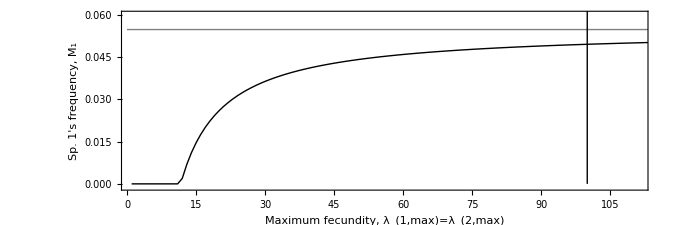

```mathematica
Show[
ListPlot[{freq1res01List[[All,2]],freq1res02List[[All,2]],Table[ {200(i-1)/100,0.0547311264053863},{i,1,101}]},
PlotRange->{{1,111},{-0.001,0.06}},Joined->True,PlotStyle->{{Black,Thick},{Black,Thick},{Gray,Thick}},Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{RowBox[{"Sp","."," ",RowBox[{"1","'"}]}],"s"," ","frequency"}],","," ",SubscriptBox[StyleBox["M",FontSlant->"Italic"],"1"]}]],None},{RawBoxes[RowBox[{RowBox[{"Maximum"," ","fecundity"}],","," ",RowBox[{SubscriptBox[StyleBox["λ",FontSlant->"Italic"],RowBox[{"1",",","max"}]],"=",SubscriptBox[StyleBox["λ",FontSlant->"Italic"],RowBox[{"2",",","max"}]]}]}]],None}},PlotLabel->None,LabelStyle->{18,GrayLevel[0]}],
Graphics[Line[{{100,0},{100,1}}]],AspectRatio->1/3
]
```

## Figure (d, e) Nullcline 3D

### Demography

```mathematica
N1tPlus1MinusN1=(lambdaMax01 Exp[-(x1-xopt)^2])/(1+N1+betaMax Exp[-(x2-x1)^2] N2)-1;
N1tPlus1N1=(lambdaMax01 Exp[-(x1-xopt)^2])/(1+N1+betaMax Exp[-(x2-x1)^2] N2);
N2tPlus1MinusN2=(lambdaMax02 Exp[-(x2-xopt)^2])/(1+N2+betaMax Exp[-(x1-x2)^2]N1)-1;
```

### Evolution

```mathematica
x1tPlus1MinusX1=D[Log[N1tPlus1N1],x1]//Simplify
```

-(2 (ⅇ^((x1-x2)^2) (1+N1) (x1-xopt)+betaMax N2 (x2-xopt)))/(ⅇ^((x1-x2)^2) (1+N1)+betaMax N2)

### Contourplot (lambdaMax01 = 100)

```mathematica
par={x2->-0.1,xopt->0,lambdaMax01->100,lambdaMax02->100,betaMax->1.1};
xMax=100;

fr01=FindRoot[{(N1tPlus1MinusN1/.par)==0,(N2tPlus1MinusN2/.par)==0,(x1tPlus1MinusX1/.par)==0},{N1,5},{N2,95},{x1,0.8}]
fr02=FindRoot[{(N1tPlus1MinusN1/.par)==0,(N2tPlus1MinusN2/.par)==0,(x1tPlus1MinusX1/.par)==0},{N1,100},{N2,0},{x1,0}]
```

{N1→4.98114,N2→95.5339,x1→0.79237}

{N1→48.0052,N2→47.3096,x1→0.10195}

```mathematica
Show[
ContourPlot3D[{(N1tPlus1MinusN1/.par)==0,(N2tPlus1MinusN2/.par)==0,(x1tPlus1MinusX1/.par)==0},{N1,0,100},{N2,0,100},{x1,0,1},Mesh->None,ContourStyle->{RGBColor[1,0,0,0.3],RGBColor[0,0,1,0.3],RGBColor[0,1,0,0.3]}],
Graphics3D[{Red,Ellipsoid[{fr01[[1,2]],fr01[[2,2]],fr01[[3,2]]},{3,3,0.03}]}],Graphics3D[{Gray,Ellipsoid[{fr02[[1,2]],fr02[[2,2]],fr02[[3,2]]},{3,3,0.03}]}],
Graphics3D[{Red,Ellipsoid[{100,0,0},{3,3,0.03}]}],
AxesLabel->{"Species 1's density, N_1","Species 2's density, N_2","Species 1's trait, x_1"},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

-Graphics3D-

```mathematica
Show[
ContourPlot3D[{N1==0,(N1tPlus1MinusN1/.par)==0,(N2tPlus1MinusN2/.par)==0,(x1tPlus1MinusX1/.par)==0},{N1,0,100},{N2,0,100},{x1,0,1},Mesh->None,ContourStyle->{RGBColor[1,0,0,0.3],RGBColor[1,0,0,0.3],RGBColor[0,0,1,0.3],RGBColor[0,1,0,0.3]}],
Graphics3D[{Red,Ellipsoid[{fr01[[1,2]],fr01[[2,2]],fr01[[3,2]]},3{1,1,0.01}]}],Graphics3D[{Gray,Ellipsoid[{fr02[[1,2]],fr02[[2,2]],fr02[[3,2]]},3{1,1,0.01}]}],
Graphics3D[{Red,Ellipsoid[{100,0,0},3{1,1,0.01}]}],LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

-Graphics3D-

### Contourplot (lambdaMax01 = 5)

```mathematica
par={x2->-0.1,xopt->0,lambdaMax01->5,lambdaMax02->5,betaMax->1.1};
xMax=100;

fr01=FindRoot[{(N1tPlus1MinusN1/.par)==0,(N2tPlus1MinusN2/.par)==0,(x1tPlus1MinusX1/.par)==0},{N1,1},{N2,5},{x1,0.8}]
```

{N1→-0.338708,N2→4.21238,x1→0.492972}

```mathematica
fr02=FindRoot[{(N1tPlus1MinusN1/.par)==0,(N2tPlus1MinusN2/.par)==0,(x1tPlus1MinusX1/.par)==0},{N1,1},{N2,1},{x1,0}]
```

{N1→1.77482,N2→2.05955,x1→0.0790686}

```mathematica
Show[
ContourPlot3D[{N1==0,(N1tPlus1MinusN1/.par)==0,(N2tPlus1MinusN2/.par)==0,(x1tPlus1MinusX1/.par)==0},{N1,0,5},{N2,0,5},{x1,0,0.6},Mesh->None,ContourStyle->{RGBColor[1,0,0,0.3],RGBColor[1,0,0,0.3],RGBColor[0,0,1,0.3],RGBColor[0,1,0,0.3]}],
(*Graphics3D[{Red,Ellipsoid[{fr01[[1,2]],fr01[[2,2]],fr01[[3,2]]},0.2{1,1,0.12}]}],*)Graphics3D[{Gray,Ellipsoid[{fr02[[1,2]],fr02[[2,2]],fr02[[3,2]]},0.2{1,1,0.12}]}],
Graphics3D[{Red,Ellipsoid[{5,0,0},0.2{1,1,0.12}]}],LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]},
AxesLabel->{"Species 1's density, N_1","Species 2's density, N_2","Species 1's trait, x_1"}
]
```

-Graphics3D-

```mathematica
Show[
ContourPlot3D[{N1==0,(N1tPlus1MinusN1/.par)==0,(N2tPlus1MinusN2/.par)==0,(x1tPlus1MinusX1/.par)==0},{N1,0,5},{N2,0,5},{x1,0,0.6},Mesh->None,ContourStyle->{RGBColor[1,0,0,0.3],RGBColor[1,0,0,0.3],RGBColor[0,0,1,0.3],RGBColor[0,1,0,0.3]}],
(*Graphics3D[{Red,Ellipsoid[{fr01[[1,2]],fr01[[2,2]],fr01[[3,2]]},0.2{1,1,0.12}]}],*)Graphics3D[{Gray,Ellipsoid[{fr02[[1,2]],fr02[[2,2]],fr02[[3,2]]},0.15{1,1,0.12}]}],
Graphics3D[{Red,Ellipsoid[{5,0,0},0.15{1,1,0.12}]}],LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

-Graphics3D-

## Figure (f, g, h, i) Simulation (Late immigration of sp. 2) (λ_(i,max)=5)

### Demography

```mathematica
N1tPlus1=(lambdaMax01 Exp[-(x1-xopt)^2]N1)/(1+N1+betaMax Exp[-(x2-x1)^2] N2);
N1tPlus1N1=(lambdaMax01 Exp[-(x1-xopt)^2])/(1+N1+betaMax Exp[-(x2-x1)^2] N2);
N2tPlus1=(lambdaMax02 Exp[-(x2-xopt)^2]N2)/(1+N2+betaMax Exp[-(x1-x2)^2]N1);
```

### Evolution

```mathematica
x1tPlus1=x1+G D[Log[N1tPlus1N1],x1]//Simplify
```

(-ⅇ^((x1-x2)^2) (1+N1) ((-1+2 G) x1-2 G xopt)+betaMax N2 (x1+2 G (-x2+xopt)))/(ⅇ^((x1-x2)^2) (1+N1)+betaMax N2)

### Simulation

```mathematica
par={x2->-0.1,xopt->0,lambdaMax01->5,lambdaMax02->5,betaMax->1.1,G->0.01};
var={N1->N1[t],N2->N2[t],x1->x1[t]};
```

```mathematica
(* population dynamics *)
f1=N1tPlus1/.var;
f2=N2tPlus1/.var;
f3=x1tPlus1/.var;
```

```mathematica
tend01=15;

(* initial values *)
init={N1[0]==(lambdaMax01 Exp[-0.5^2]-1/.par),N2[0]==0,x1[0]==0.5};
flow={N1[t+1]==f1/.par,N2[t+1]==f2/.par,x1[t+1]==f3/.par};

(* simulation *)
sol01=RecurrenceTable[Join[flow,init],{N1,N2,x1},{t,0,tend01}];
```

```mathematica
tMax=1000;
tend02=tMax-tend01;

(* initial values *)
init={N1[0]==sol01[[tend01,1]],N2[0]==sol01[[tend01,1]]/9,x1[0]==sol01[[tend01,3]]};
flow={N1[t+1]==f1/.par,N2[t+1]==f2/.par,x1[t+1]==f3/.par};
(* simulation *)
sol02=RecurrenceTable[Join[flow,init],{N1,N2,x1},{t,0,tend02}];
```

### Population dynamics

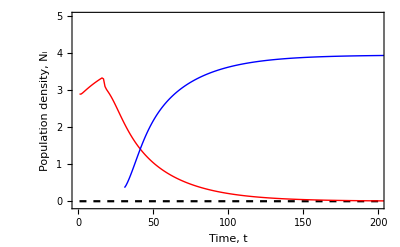

```mathematica
yMax=lambdaMax01/.par;
N20List={};Do[N20List=Append[N20List,{n-1,NA}],{n,tend01}];
N1List=Flatten[{ sol01[[All,1]],sol02[[All,1]]}];
N1List=Table[{n-1,N1List[[n]]},{n,tMax}];
N2List=Flatten[{ N20List,sol02[[All,2]]}];
N2List=Table[{n-1,N2List[[n]]},{n,tMax}];
zeroList={};Do[zeroList=Append[zeroList,0],{n,Length[N1List]}];

ListPlot[
{zeroList,Flatten[{ sol01[[All,1]],sol02[[All,1]]}],Flatten[{ N20List,sol02[[All,2]]}]},Joined->True,
PlotRange-> {{0,200},{-0.1,yMax}},
PlotStyle->{{Black,Dashed},{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Population"," ","density"}],","," ",StyleBox[SubscriptBox["N","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

### Mean trait dynamics

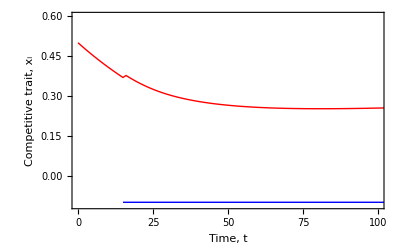

```mathematica
yMax=0.6;
x1List=Flatten[{sol01[[All,3]],sol02[[All,3]]}];
x1List=Table[{n-1,x1List[[n]]},{n,tMax}];
x20List={};Do[x20List=Append[x20List,NA],{n,tend01}];
x21List={};Do[x21List=Append[x21List,x2/.par],{n,tend02}];
x2List=Flatten[{x20List,x21List}];
x2List=Table[{n-1,x2List[[n]]},{n,tMax}];
x1ListDensity=Flatten[{sol01[[All,3]],sol02[[All,3]]}];
x1ListDensity=Table[{n-1,x1ListDensity[[n]]},{n,tMax}];

ListPlot[
{(*xOptList,*)x1List,x2List},Joined->True,
PlotRange-> {{0,100},{-0.11,yMax}},
PlotStyle->{(*RGBColor[0,0.45,0],*){Red,Thick},{Blue,Thick}},Frame->True,LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]},FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Competitive"," ","trait"}],","," ",StyleBox[SubscriptBox["x","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},PlotLabel->None
]
```

### Simulation (Frequency dynamics)

#### Base equation (Demography)

```mathematica
M1tPlus1=((lambdaMax01 Exp[-(x1-xopt)^2]M1)/(M1+betaMax Exp[-(x2-x1)^2] (1-M1)))/((lambdaMax01 Exp[-(x1-xopt)^2]M1)/(M1+betaMax Exp[-(x2-x1)^2] (1-M1))+(lambdaMax02 Exp[-(x2-xopt)^2](1-M1))/((1-M1)+betaMax Exp[-(x1-x2)^2]M1));
```

#### Base equation (Evolution)

```mathematica
D[Log[(lambdaMax01 Exp[-(x1-xopt)^2])/(N1+betaMax Exp[-(x2-x1)^2] N2)],x1]
```

1/lambdaMax01 ⅇ^((x1-xopt)^2) (N1+betaMax ⅇ^(-(-x1+x2)^2) N2) (-(2 betaMax ⅇ^(-(-x1+x2)^2-(x1-xopt)^2) lambdaMax01 N2 (-x1+x2))/((N1+betaMax ⅇ^(-(-x1+x2)^2) N2)^2)-(2 ⅇ^(-(x1-xopt)^2) lambdaMax01 (x1-xopt))/(N1+betaMax ⅇ^(-(-x1+x2)^2) N2))

```mathematica
x1tPlus1=x1+G 1/lambdaMax01 ⅇ^((x1-xopt)^2) (M1+betaMax ⅇ^(-(-x1+x2)^2) (1-M1)) (-(2 betaMax ⅇ^(-(-x1+x2)^2-(x1-xopt)^2) lambdaMax01 (1-M1) (-x1+x2))/((M1+betaMax ⅇ^(-(-x1+x2)^2) (1-M1))^2)-(2 ⅇ^(-(x1-xopt)^2) lambdaMax01 (x1-xopt))/(M1+betaMax ⅇ^(-(-x1+x2)^2) (1-M1)));
```

### Simulation (Late immigration of sp. 2) (λ_(i,max)=5)

```mathematica
par={x2->-0.1,xopt->0,lambdaMax01->5,lambdaMax02->5,betaMax->1.1,G->0.01};
var={M1->M1[t],x1->x1[t]};
```

```mathematica
(* population dynamics *)
f1=M1tPlus1/.var;
f2=x1tPlus1/.var;
```

```mathematica
tend01=15;

(* initial values *)
init={M1[0]==1,x1[0]==0.5};
flow={M1[t+1]==f1/.par,x1[t+1]==f2/.par};

(* simulation *)
sol01=RecurrenceTable[Join[flow,init],{M1,x1},{t,0,tend01}];
```

```mathematica
tend02=tMax-tend01;

(* initial values *)
init={M1[0]==0.9,x1[0]==sol01[[tend01,2]]};
flow={M1[t+1]==f1/.par,x1[t+1]==f2/.par};
(* simulation *)
sol02=RecurrenceTable[Join[flow,init],{M1,x1},{t,0,tend02}];
```

### Population dynamics

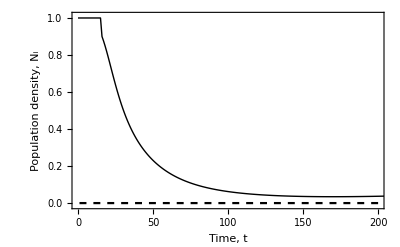

```mathematica
yMax=1.01;
N20List={};Do[N20List=Append[N20List,NA],{n,tend01}];
freq01List=Flatten[{ sol01[[All,1]],sol02[[All,1]]}];
freq01List=Table[{n-1,freq01List[[n]]},{n,tMax}];

ListPlot[
{zeroList,freq01List},Joined->True,
PlotRange-> {{0,200},{-0.01,yMax}},
PlotStyle->{{Black,Dashed},{Black,Thick}},Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Population"," ","density"}],","," ",StyleBox[SubscriptBox["N","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

### Mean trait dynamics

```mathematica
x1ListFreq=Flatten[{ sol01[[All,2]],sol02[[All,2]]}];
x1ListFreq=Table[{n-1,x1ListFreq[[n]]},{n,tMax}];
```

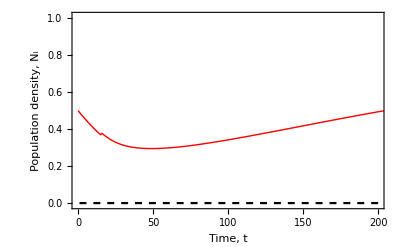

```mathematica
ListPlot[
{zeroList,x1ListFreq},Joined->True,
PlotRange-> {{0,200},{-0.01,yMax}},
PlotStyle->{{Black,Dashed},{Red,Thick}},Frame->True,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Population"," ","density"}],","," ",StyleBox[SubscriptBox["N","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}
]
```

### Overlaying population & frequency dynamics

```mathematica
yScale=lambdaMax01/.par;yMin=0.05;
scaledFreq01List=Table[{n-1,yScale freq01List[[n,2]]},{n,tMax}];
```

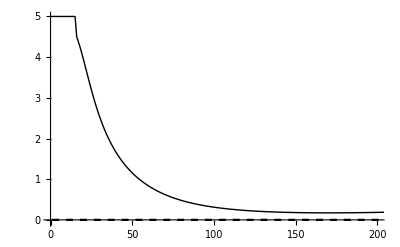

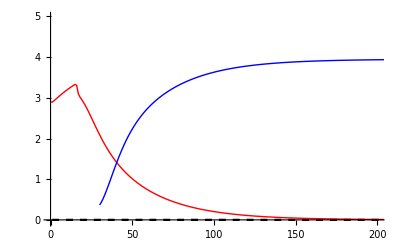

```mathematica
l2=ListPlot[
{zeroList,scaledFreq01List},Joined->True,
PlotRange-> {{0,200},{-yMin,yScale}},
PlotStyle->{{Black,Dashed},{Black,Thick}}
]

l1=ListPlot[
{zeroList,N1List,N2List},Joined->True,
PlotRange-> {{0,200},{-yMin,yScale}},
PlotStyle->{{Black,Dashed},{Red,Thick},{Blue,Thick}}
]
```

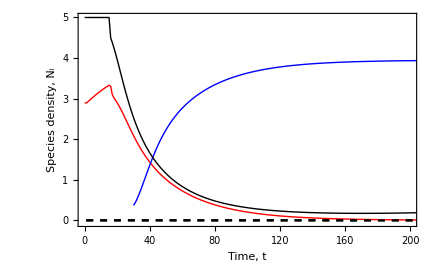

```mathematica
Show[l1,l2,Frame->True,FrameTicks->{{All,{{0,"0"},{0.2 yScale,"0.2"},{0.4 yScale,"0.4"},{0.6 yScale,"0.6"},{0.8 yScale,"0.8"},{yScale,"1"}}},{All,None}},FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Species"," ","density"}],","," ",StyleBox[SubscriptBox["N","i"],FontSlant->"Italic"]}]],RawBoxes[RowBox[{RowBox[{"Sp. 1's"," ","frequency"}],","," ",SubscriptBox[StyleBox["M",FontSlant->"Italic"],"1"]}]]},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}]
```

```mathematica
xOptList={};Do[xOptList=Append[xOptList,0],{n,Length[N1List]}];
```

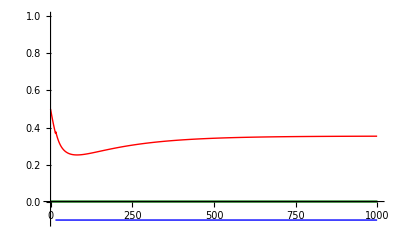

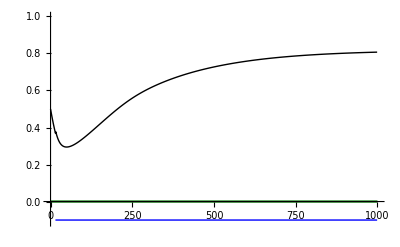

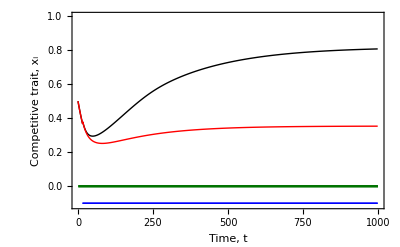

```mathematica
yMax=1.;
l2=ListPlot[
{xOptList,x1ListDensity,x2List},Joined->True,
PlotRange-> {{0,tMax},{-0.11,yMax}},
PlotStyle->{RGBColor[0,0.45,0],{Red,Thick},{Blue,Thick}}
]

l1=ListPlot[
{xOptList,x1ListFreq,x2List},Joined->True,
PlotRange-> {{0,tMax},{-0.11,yMax}},
PlotStyle->{RGBColor[0,0.45,0],{Black,Thick},{Blue,Thick}}
]

Show[l1,l2,Frame->True,LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]},FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Competitive"," ","trait"}],","," ",StyleBox[SubscriptBox["x","i"],FontSlant->"Italic"]}]],None},{RawBoxes[RowBox[{"Time",","," ",StyleBox["t",FontSlant->"Italic"]}]],None}},PlotLabel->None]
```